## Computing for Mathematical Physics 2022/23

# Homework 5

# Mark for homework 5: 26/32 but unfortunately over 10 days too late. (to be competed by your marker)

# Feedback from marker: Q1: 11/14. Q2: 8/9. Q3: 5/5. Q4: 2/4 (note, the marking scheme is deliberately strict in Q4). Good answers, losing marks to just relatively minor issues, which you could catch with a little more time/care/attention to detail. See my comments in purple under your answers throughout the script below for more information on these. The main message, looking ahead to these last 2-3 weeks of the course+exam, is that you can do this. (to be competed by your marker)

# Give your answers in the code cells marked (* Enter your solution here *)

Double click the vertical braces on the RHS of each of the question headings to open and view them.

1. Plotting multiple functions on the same graph, labeled, and legended.  [14 marks]

a) Define the wavefunction ψ[n_,x_] in your code according to  
	ψ_n(x) = 1/(√(2^n n!))1/π^(1/4)e^(-1/2 x^2)H_n(x) ,
wherein H_n(x) are the Hermite polynomials, implemented in Mathematica as HermiteH[n,x].

b) Plot ψ_n(x) for n=1,2,3, over the range -5 ≤ x ≤ 5.

• Fix the y-axis range to -0.7 ≤ y ≤ 0.7.
• Use a different colour for each of the three lines plotted.
• Label the axes.
• Include a title “Wavefunctions ψ_n(x)” 
• Include a legend indicating clearly what each line represents.
• Place the legend in the top right of the graph.
• Use LabelStyle to set the Times font family, in Black, with font size 18, for all textual elements.
• Use grid lines.

[14 marks]

```mathematica
ψ[n_, x_]:=1/(√(2^n n!))1/π^0.25 ⅇ^(-0.5 x^2)HermiteH[n,x]
(*Create function for phi*)
```

```mathematica
n = {1, 2,3}
```

{1,2,3}

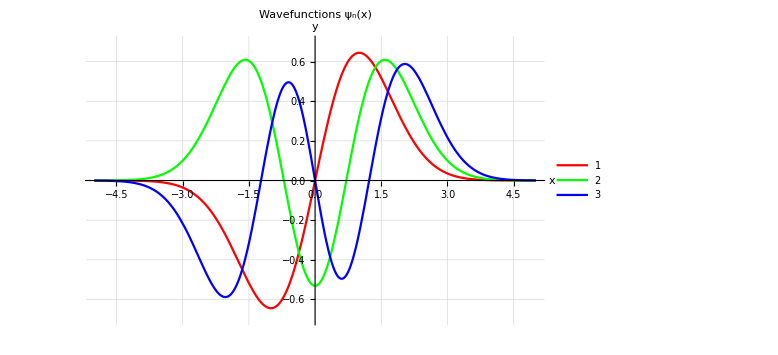

Information[Placed[{1,2,3},{1,1}],LongForm→False]

```mathematica
Plot[Evaluate[Thread[ψ[n, x]]], (*use the function and thread so that all graphs for all values of n can be created*)
{x,-5,5},(*Define Range for x values*)
PlotLabel->"Wavefunctions ψ_n(x)",(*Label Graph*)
 PlotRange->{-0.7, 0.7},(*set limit for y axis*)
PlotLegends->Placed[{"1","2","3"},{0.9,0.85}],(*Create legend and place in the top right of the graph*)
 AxesLabel->{"x","y"},(*Label Axis*)
PlotStyle->Table[{Hue[i]},{i,0,1,1/Length[n]}],(*Give each line a different colour*)
LabelStyle->{Black,Times, FontSize->18},(*Give style for each line*)
 GridLines->Automatic,(*Add gridlines*)
 ImageSize->Large (*make image large but that hasnt worked*)
]
?Placed[{"1","2","3"},{1,1}]
```

• Question 1: 11/14
• Good effort.
• Lost 1 mark for not getting the font right: you just need replace Times by FontFamily->”Times” in LabelStyle.
• Lost 1 mark for not labelling y-axis as "ψ_n(x)".
• Lost 1 mark for the legend contents being unclear/abstract (“1”, “2”, “3”).
• Please, see also my answer below for an alternative perspective, with slightly more standard ways of doing things, e.g. providing multiple functions to plot inside a single plot command.

```mathematica
(* Marker/Coordinator's code here *)

(* Part a *)
(* Defining Subscript[ψ, n](x) as written in the question *)
ψ[n_,x_]:=1/(√(2^n n!))1/π^(1/4)Exp[-1/2 x^2]HermiteH[n,x]

(* Part b *)
Plot[
(* We are directed to plot Subscript[ψ, n](x) for n = 1, 2, 3 *)
{
ψ[1,x],
ψ[2,x],
ψ[3,x]
},

(* Question asks us to plot the x range -5 ≤ x ≤ 5 *)
{x,-5,5},

(* Fix the y-axis range to -0.7 ≤ y ≤ 0.7 *)
PlotRange->{-0.7,0.7},

(* Use a different colour for each of the three lines plotted *)
PlotStyle->{Red,Green,Blue},

(* Label the axes *)
AxesLabel->{"x","ψ_n(x)"},

(* Include the title "Wavefunctions ψ_n(x)" *)
PlotLabel->"Wavefunctions ψ_n(x)\n",

(* Include a legend indicating clearly what each line *)
(* represents placing the legend in the top right of  *)
(* the graph *)
PlotLegends->Placed[LineLegend["Expressions"],{1.0,0.85}],

(* Use LabelStyle to Set the overall font style *)
LabelStyle->{FontFamily->"Times",FontColor->Black,FontSize->18},

(* Finally we introduce  the grid lines *)
GridLines->Automatic
]
```

2. Primitive graphics animation. [9 marks]

Point[{x,y}] is a Graphics primitive which represents a point at the position (x,y).
PointSize[...] is a function which sets the size of the point.

Write a piece of code which will represent, as an animation, the motion of a ball oscillating in a harmonic potential well, according to the following steps.

a) Plot y=x^2 over the range -2≤x≤2, with the y axis range limited to -0.2 ≤ y ≤ 4.2, to represent the potential well. Give the plot a frame and gridlines. Call this plot potentialWell.

b) Write a function ballPosition[t_], returning the coordinates, {x,y}, of the the ball at time t, as it oscillates in the potential well. The x coordinate evolves in time according to x = 2 cos(2t), with the corresponding  y coordinate given by the shape of the well in which the ball oscillates.

c) Use Show, inside Animate, to combine the potentialWell plot together with a Graphics object made from a Point, whose position argument is given by ballPosition[t]. Consider which range of values for t will give you a complete cycle in your animation, and select an appropriate time-step.

[Hint: you may need to check Evaluation→Dynamic Updating Enabled is selected in the drop-down menus.]
[9 marks]

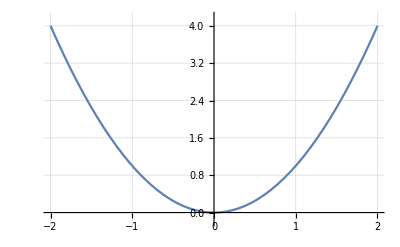

```mathematica
potentialWell =Plot[x^2,{x,-2,2}, PlotRange->{-0.2, 4.2},GridLines->Automatic]
(*for some reason, adding a frame stops the animation from working*)
```

```mathematica
ballPosition[t_]:={2Cos[2t],(2Cos[2t])^2} (*parametric equation for the ball*)
```

```mathematica
Animate[Show[Graphics[Point[ballPosition[x]]], potentialWell],{x,0,π,0.01}](*show both the well and the ball inside of it*)
```

• Question 2: 8/9
• Good work. 
• One minor problem here is that you should have taken the hint to use PointSize[...] at the start of the question to make the moving ball bigger .
• Also if you had interchanged the order of the well and the ball inside Show[...] the gridlines and axes of the well would have become visible, as in the edited code I supply in the next input cell:

```mathematica
(* Coordinator's edited version of your code here. *)
Animate[Show[potentialWell,Graphics[{PointSize[0.03],Point[ballPosition[x]]}]],{x,0,π,0.01}](*show both the well and the ball inside of it*)
```

3. Approximate root-finding using Plot. [5 marks]

Use Plot to determine the value of x, between 0 and 10, to 3 significant figures, which solves the equation Log[1/x] == Tanh[x] as follows. Make a Plot showing both Log[1/x] and Tanh[x], and then manually refine the x range (as given in the second argument of Plot), repeatedly, so as to zoom in on the point where the two lines intersect.

You need only display the final plot in the series of plots leading to your final answer. Your answer should be written in a text cell to 3 significant figures.
[5 marks]

Turns out I read the question wrong, I could’ve made my life much easier using just the plot function

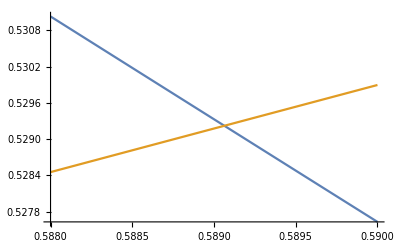

```mathematica
Plot[{Log[1/x], Tanh[x]},{x,0.588,0.590}](*Adjust the range until intersection can be seen at a very precise reading*)
```

The answer is 0.589 to three significant figures.

• Question 3: 5/5
• Correct.

4. Primitive graphics animation revisited. [4 marks]

This question generalises question 2.

Define a potential V[x_] := 34/31-x^2+x^3+x^4.

a) Plot V[x] over the range -2.5≤x≤2.5, limiting the y-axis range shown to 0≤y≤6.
     Give the plot a frame and gridlines.
     Call this plot q4Well.

b) The equation of motion for a particle moving along the x-axis under the influence of this potential is given by 
       d^2/(d t^2)x[ t ] = -d/(d x)V[ x[ t ] ] 
     where x[t]  is the particle’s position at time t.
     Use NDSolve to solve the equation of motion for  x[t] subject to the boundary conditions 
           x[0] = -2
    x’[0] = 0
     for t in the range 0<t<20.

c) Write a function particle[t_], returning {x[t], V[x[t]]}, with x[t] given by the solution to part b) .

d) Use Show, inside Animate, to combine the q4Well plot together with a Graphics object made from a Point, whose position argument is given by particle[t]. Adjust the animation rate until it is smooth using the AnimationRate option.

[Hint: depending on your approach, it may help to define  particle[t_] with Set, i.e. =, rather than SetDelayed, i.e. :=.]

[4 marks : only fully functioning, correct, solutions for this question are eligible for marks.]

```mathematica
V[x_]:= 34/31 - x^2+x^3+x^4
```

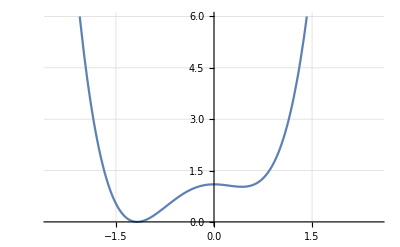

```mathematica
q4Well = Plot[V[x],{x, -2.5, 2.5},PlotRange->{0,6}, GridLines->Automatic](*Once again, the framed option stops my animation from working*)
```

```mathematica
NDSolve[{x''[t]==-V'[x[t]],x[0]==-2, x'[0]==0},x[t],{t,0,20}]
```

{{x(t)→InterpolatingFunction[…](t)}}

```mathematica
particle[t_]:={InterpolatingFunction[…][t],V[InterpolatingFunction[…][t]]} (*using set or setDelayed makes no difference, at least for my simulation*)
```

```mathematica
Animate[Show[Graphics[Point[particle[x]]], q4Well],{x,0,π,0.01}]
```

• Question 4: 2/4
• Same issue as in Q2 : the moving point/ball is obviously too small/too hard to see.
• Also if you had interchanged the order of the well and the ball inside Show[...] the gridlines and axes of the well would have become visible, as in the edited code I supply in the next input cell:

```mathematica
(* Coordinator's edited version of your code: *)
Animate[Show[q4Well,Graphics[{PointSize[0.03],Point[particle[x]]}]],{x,0,π,0.01}]
```

Total marks available: 32

Solutions are due by 1200 noon on Thursday February 23rd here:  allow time for uploading on moodle.

A 10% mark deduction will be made (3 marks) if the template isn’t used.

Name your solution notebook file in the format WK5_HMWK_<Initials>_<Family Name>.nb, e.g. WK5_HMWK_K_Hamilton.nb

Make a backup copy of your solutions.

Delete all cell evaluation output by selecting Cell → Delete All Output from the drop-down menus at the top of the screen, then save and upload that file to Moodle.

The first thing your marker will do when they receive your notebook is to evaluate all of it, to regenerate the output, by clicking Evaluation → Evaluate Notebook from the drop-down menus at the top of the screen. It is your responsibility to check that carrying out this process with a fresh kernel will produce the output you intend it to, before you upload your work.

K. Hamilton
J. Bhamrah, J. Underwood, A. Harker 
Last revision 13:33 07 Feb 2023